```mathematica
U = -3/2x^5+5/2x^3
```

(5 x^3)/2-(3 x^5)/2

```mathematica
(*Derivata prima dell' energia potenziale*)
DU=D[U,x]
```

(15 x^2)/2-(15 x^4)/2

```mathematica
(*Punti critici dell'energia*)
CPP=Solve[DU== 0,x,Reals]
```

{{x→-1},{x→0},{x→0},{x→1}}

```mathematica
(*Valutazione dell' energia nei suoi punti critici*)
CP = U /.CPP
```

{-1,0,0,1}

```mathematica
(*Derivata seconda del potenziale*)
DDU = D[DU,x]
```

15 x-30 x^3

```mathematica
(*Punti di flesso del potenziale*)
 FLP = Solve[DDU == 0, x]
```

{{x→0},{x→-1/(√2)},{x→1/(√2)}}

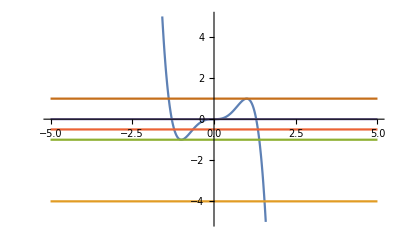

```mathematica
(*Energia Potenziale*)

Plot[{U,-4,-1,-1/2,0,1},{x,-5,5}, PlotRange ->{-5,5}]
```

{√2 √(EE-(5 x^3)/2+(3 x^5)/2),-√2 √(EE-(5 x^3)/2+(3 x^5)/2)}

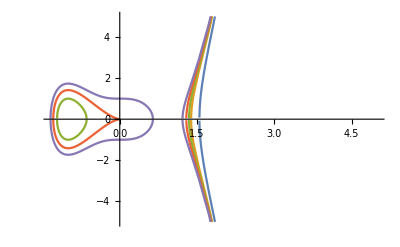

```mathematica
(*Curve di livelo*)
Cvl = {Sqrt[2*(EE-U)], -Sqrt[2*(EE-U)]}
(*Piano delle fasi*)
Plot[{Cvl /. EE -> -4,
	Cvl /. EE -> -1,
	Cvl /. EE -> -1/2,
         Cvl /. EE -> 0,
	Cvl /. EE -> 1/2
},{x,-5,5}, PlotRange ->{-5,5}]
```

```mathematica
DDU /. x -> -1
DDU /. x -> 0
DDU /. x -> 1
```

15

0

-15